### Perceptron Convergence Theorem-Numerical Illustration

We work in ℝ.b2 and construct data that is linearly separable by a "teacher" hyperplane (w^*,b^*).

```mathematica
ClearAll[generateSeparableData]
```

```mathematica
generateSeparableData[nSamples_,dim_,margin_]:=Module[{wStar,bStar,x,m,label,X={},y={}},(*Random but fixed separator*)wStar=Normalize[RandomReal[NormalDistribution[0,1],dim]];
bStar=RandomReal[NormalDistribution[0,0.1]];
While[Length[X]<nSamples,x=RandomVariate[NormalDistribution[0,1],dim];
m=wStar.x+bStar;
If[Abs[m]<margin,Continue[]];
label=If[m>0,1,-1];
AppendTo[X,x];
AppendTo[y,label];];
<|"X"->X,"y"->y,"wStar"->wStar,"bStar"->bStar|>]
```

```mathematica
data=generateSeparableData[60, 2, 0.5]
```

<|X→{{-0.918827,0.328277},{0.896931,-0.511499},{-1.91722,1.14654},{-0.921779,0.759588},{-1.66206,-0.777004},{1.17185,1.76566},{0.951345,-0.668982},{2.72712,1.89158},{-1.37592,-0.774256},{1.61827,1.09772},{0.406804,-0.788894},{0.667785,-0.537029},{1.11135,-0.366609},{-1.20144,0.761085},{0.349275,0.432279},{0.320296,1.16912},{1.181,-0.518478},{0.714623,-0.320661},{1.34284,-1.15242},{2.12367,0.598975},{0.506765,0.568557},{-1.68923,0.354126},{-0.639955,-2.03667},{-1.52843,-1.19515},{0.815272,-0.213358},{1.78284,0.746603},{1.35021,-1.33661},{-0.959666,-1.26628},{-0.582507,-1.81254},{1.0725,1.38188},{-1.45057,-0.891523},{-1.18203,0.261622},{0.956198,1.32246},{0.557256,0.3535},{-1.33144,-2.14452},{1.43496,-0.185219},{-1.54262,0.371613},{-1.25171,-1.01187},{-2.01716,-2.3809},{1.86268,0.24762},{0.515905,0.833914},{-1.28301,-0.696348},{0.977386,-1.76019},{0.685412,-0.980613},{0.613276,1.05961},{0.607008,-0.909467},{1.76251,1.41203},{-1.76897,-0.639123},{-0.931938,1.33625},{1.06187,0.818752},{0.534002,-0.040019},{0.53423,-1.1931},{1.13788,-3.00486},{-1.39535,-0.949252},{1.00104,-0.823306},{0.663107,2.56425},{1.33745,-0.252797},{0.475141,-1.12622},{-0.895608,0.721624},{-0.969467,0.474014}},y→{-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,-1,-1,-1,1,1,-1,1,1,1,1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,-1},wStar→{0.998399,0.0565556},bStar→0.181843|>

```mathematica
X=data["X"]
```

{{-0.918827,0.328277},{0.896931,-0.511499},{-1.91722,1.14654},{-0.921779,0.759588},{-1.66206,-0.777004},{1.17185,1.76566},{0.951345,-0.668982},{2.72712,1.89158},{-1.37592,-0.774256},{1.61827,1.09772},{0.406804,-0.788894},{0.667785,-0.537029},{1.11135,-0.366609},{-1.20144,0.761085},{0.349275,0.432279},{0.320296,1.16912},{1.181,-0.518478},{0.714623,-0.320661},{1.34284,-1.15242},{2.12367,0.598975},{0.506765,0.568557},{-1.68923,0.354126},{-0.639955,-2.03667},{-1.52843,-1.19515},{0.815272,-0.213358},{1.78284,0.746603},{1.35021,-1.33661},{-0.959666,-1.26628},{-0.582507,-1.81254},{1.0725,1.38188},{-1.45057,-0.891523},{-1.18203,0.261622},{0.956198,1.32246},{0.557256,0.3535},{-1.33144,-2.14452},{1.43496,-0.185219},{-1.54262,0.371613},{-1.25171,-1.01187},{-2.01716,-2.3809},{1.86268,0.24762},{0.515905,0.833914},{-1.28301,-0.696348},{0.977386,-1.76019},{0.685412,-0.980613},{0.613276,1.05961},{0.607008,-0.909467},{1.76251,1.41203},{-1.76897,-0.639123},{-0.931938,1.33625},{1.06187,0.818752},{0.534002,-0.040019},{0.53423,-1.1931},{1.13788,-3.00486},{-1.39535,-0.949252},{1.00104,-0.823306},{0.663107,2.56425},{1.33745,-0.252797},{0.475141,-1.12622},{-0.895608,0.721624},{-0.969467,0.474014}}

```mathematica
y=data["y"]
```

{-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,1,1,1,1,1,-1,-1,-1,1,1,1,-1,-1,1,-1,-1,1,1,-1,1,-1,-1,-1,1,1,-1,1,1,1,1,1,-1,-1,1,1,1,1,-1,1,1,1,1,-1,-1}

```mathematica
wStar=data["wStar"]
```

{0.998399,0.0565556}

```mathematica
bStar=data["bStar"]
```

0.181843

```mathematica
Dimensions[X]
```

{60,2}

```mathematica
Counts[y]
```

<|-1→23,1→37|>

### Plot of linearly separable data

```mathematica
pos = Pick[X, UnitStep[y], 1]
```

{{0.896931,-0.511499},{1.17185,1.76566},{0.951345,-0.668982},{2.72712,1.89158},{1.61827,1.09772},{0.406804,-0.788894},{0.667785,-0.537029},{1.11135,-0.366609},{0.349275,0.432279},{0.320296,1.16912},{1.181,-0.518478},{0.714623,-0.320661},{1.34284,-1.15242},{2.12367,0.598975},{0.506765,0.568557},{0.815272,-0.213358},{1.78284,0.746603},{1.35021,-1.33661},{1.0725,1.38188},{0.956198,1.32246},{0.557256,0.3535},{1.43496,-0.185219},{1.86268,0.24762},{0.515905,0.833914},{0.977386,-1.76019},{0.685412,-0.980613},{0.613276,1.05961},{0.607008,-0.909467},{1.76251,1.41203},{1.06187,0.818752},{0.534002,-0.040019},{0.53423,-1.1931},{1.13788,-3.00486},{1.00104,-0.823306},{0.663107,2.56425},{1.33745,-0.252797},{0.475141,-1.12622}}

```mathematica
neg = Pick[X, UnitStep[-y], 1]
```

{{-0.918827,0.328277},{-1.91722,1.14654},{-0.921779,0.759588},{-1.66206,-0.777004},{-1.37592,-0.774256},{-1.20144,0.761085},{-1.68923,0.354126},{-0.639955,-2.03667},{-1.52843,-1.19515},{-0.959666,-1.26628},{-0.582507,-1.81254},{-1.45057,-0.891523},{-1.18203,0.261622},{-1.33144,-2.14452},{-1.54262,0.371613},{-1.25171,-1.01187},{-2.01716,-2.3809},{-1.28301,-0.696348},{-1.76897,-0.639123},{-0.931938,1.33625},{-1.39535,-0.949252},{-0.895608,0.721624},{-0.969467,0.474014}}

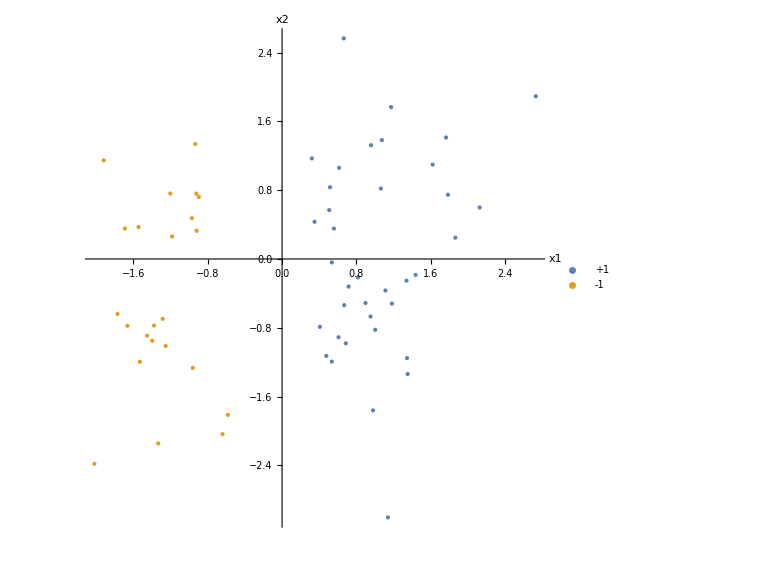

```mathematica
ListPlot[
 {
  pos,
  neg
 },
 PlotStyle -> {PointSize[Large], PointSize[Large]},
 PlotLegends -> {"+1", "-1"},
 AxesLabel -> {"x1", "x2"},
 PlotRange -> All,
 ImageSize -> Large,
 AspectRatio -> 1
]
```

### Perceptron algorithm with tracking

```mathematica
ClearAll[perceptronTrain]
```

```mathematica
perceptronTrain[X_List, y_List, maxEpochs_Integer : 1000, wStar_: None, bStar_: None] :=
 Module[{nSamples, dim, w, b, epoch, i, xi, yi, margin, mistakes,
   historyW = {}, historyB = {}, historyWDotWStar = {}, historyWNormSq = {},
   mistakesPerEpoch = {}, totalUpdates = 0, wDot},

  nSamples = Length[X];
  dim = Length[First[X]];
  w = ConstantArray[0., dim];
  b = 0.;

  For[epoch = 1, epoch <= maxEpochs, epoch++,
   mistakes = 0;
   For[i = 1, i <= nSamples, i++,
    xi = X[[i]];
    yi = y[[i]];
    margin = yi (w . xi + b);
    If[margin <= 0,
     w = w + yi xi;
     b = b + yi;
     mistakes++;
     totalUpdates++;

     If[wStar =!= None,
      wDot = w . wStar;
      AppendTo[historyWDotWStar, wDot];
      ,
      AppendTo[historyWDotWStar, Missing["NotAvailable"]];
     ];
     AppendTo[historyWNormSq, w . w];
     AppendTo[historyW, w];
     AppendTo[historyB, b];
    ];
   ];
   AppendTo[mistakesPerEpoch, mistakes];
   If[mistakes == 0, Break[]];
  ];

  <|
   "wFinal" -> w,
   "bFinal" -> b,
   "historyW" -> historyW,
   "historyB" -> historyB,
   "historyWDotWStar" -> historyWDotWStar,
   "historyWNormSq" -> historyWNormSq,
   "mistakesPerEpoch" -> mistakesPerEpoch,
   "totalUpdates" -> totalUpdates
  |>
 ]
```

```mathematica
result = perceptronTrain[X, y, 100, wStar, bStar]
```

<|wFinal→{2.13605,0.329347},bFinal→1.,historyW→{{0.918827,-0.328277},{1.81576,-0.839777},{2.13605,0.329347}},historyB→{-1.,0.,1.},historyWDotWStar→{0.898791,1.76536,2.15126},historyWNormSq→{0.95201,4.0022,4.67119},mistakesPerEpoch→{3,0},totalUpdates→3|>

```mathematica
wFinal = result["wFinal"]
```

{2.13605,0.329347}

```mathematica
bFinal = result["bFinal"]
```

1.

```mathematica
totalUpdates = result["totalUpdates"]
```

3

```mathematica
mistakesPerEpoch = result["mistakesPerEpoch"]
```

{3,0}

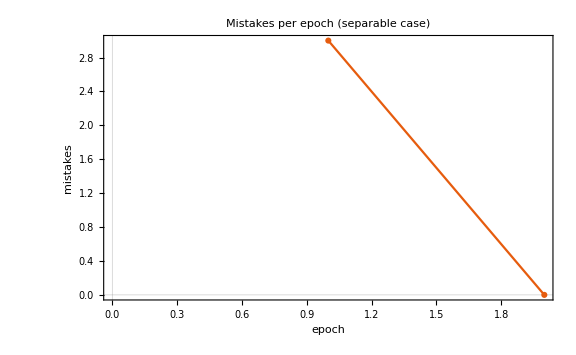

```mathematica
ListLinePlot[
 mistakesPerEpoch,
 AxesLabel -> {"epoch", "mistakes"},
 PlotMarkers -> Automatic,
 PlotTheme -> "Scientific",
 ImageSize -> Large,
 PlotLabel -> "Mistakes per epoch (separable case)"
]
```

### Decision boundary in ℝ^2

```mathematica
ClearAll[plotDecisionBoundary]
```

```mathematica
plotDecisionBoundary[w_, b_, X_, y_] :=
 Module[{pos, neg, line},
  pos = Pick[X, UnitStep[y], 1];
  neg = Pick[X, UnitStep[-y], 1];

  Show[
   ListPlot[
    {pos, neg},
    PlotStyle -> {PointSize[Large], PointSize[Large]},
    PlotLegends -> {"+1", "-1"},
    AxesLabel -> {"x1", "x2"},
    PlotRange -> All,
    AspectRatio -> 1
   ],
   (* line w.x + b == 0 => x2 = -(w1 x1 + b)/w2 *)
   If[w[[2]] != 0,
    line = Plot[
      -(w[[1]] x + b)/w[[2]],
      {x, Min[X[[All, 1]]] - 1, Max[X[[All, 1]]] + 1}
     ];
    line,
    {}
   ],
   ImageSize -> Large,
   PlotLabel -> "Perceptron decision boundary"
  ]
 ]
```

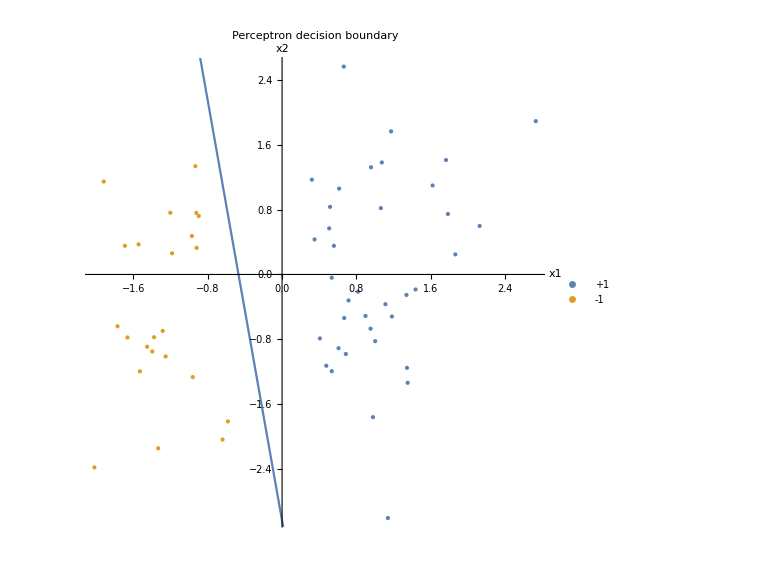

```mathematica
plotDecisionBoundary[wFinal, bFinal, X, y]
```

### R, gamma, and theoretical bound

```mathematica
norms = Norm /@ X
```

{0.97571,1.03253,2.23389,1.19442,1.83472,2.11915,1.16301,3.31892,1.5788,1.95545,0.887605,0.856935,1.17025,1.42222,0.55575,1.2122,1.2898,0.783268,1.76955,2.20653,0.761622,1.72595,2.13484,1.94023,0.842728,1.93285,1.89989,1.58885,1.90384,1.74924,1.70263,1.21063,1.63194,0.659922,2.52422,1.44686,1.58674,1.60955,3.12052,1.87906,0.980597,1.4598,2.01334,1.19641,1.22429,1.09343,2.25838,1.88089,1.62913,1.34086,0.5355,1.30724,3.21309,1.68762,1.29612,2.6486,1.36114,1.22235,1.15015,1.07915}

```mathematica
R = Max[norms]
```

3.31892

```mathematica
marginsTeacher = MapThread[#1 (#2 . wStar + bStar) &, {y, X}]
```

{0.716948,1.04841,1.66746,0.695502,1.5215,1.45167,1.09383,3.01158,1.23566,1.8596,0.543379,0.818187,1.27068,0.974631,0.555006,0.567746,1.33163,0.877187,1.45736,2.33599,0.719952,1.48466,0.572273,1.41173,0.983743,2.00405,1.4543,0.847902,0.502241,1.33078,1.31683,0.983496,1.2113,0.758199,1.26875,1.60403,1.33729,1.12509,1.96675,2.05554,0.744085,1.1385,1.05812,0.810699,0.854064,0.736443,2.02139,1.62044,0.673031,1.28831,0.712727,0.647742,1.14796,1.26496,1.13472,0.988911,1.50286,0.592529,0.67152,0.759265}

```mathematica
gamma = Min[marginsTeacher]
```

0.502241

```mathematica
bound = If[gamma > 0, (R/gamma)^2, Infinity]
<|"R" -> R, "gamma" -> gamma, "bound" -> bound, "observedUpdates" -> totalUpdates|>
```

43.6688

<|R→3.31892,gamma→0.502241,bound→43.6688,observedUpdates→3|>

```mathematica
wDotWStar = DeleteMissing[result["historyWDotWStar"]]
```

{0.898791,1.76536,2.15126}

```mathematica
wNormSq = result["historyWNormSq"]
```

{0.95201,4.0022,4.67119}

```mathematica
steps = Range[Length[wNormSq]]
```

{1,2,3}

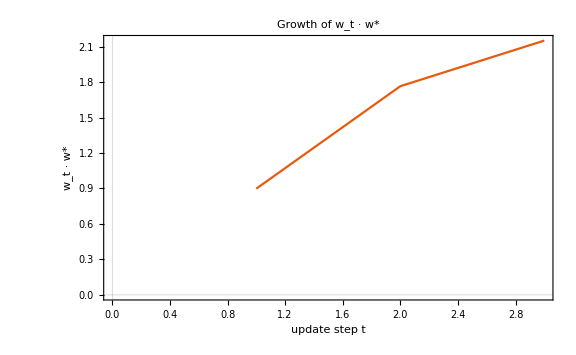

```mathematica
ListLinePlot[
 wDotWStar,
 AxesLabel -> {"update step t", "w_t · w*"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Growth of w_t · w*",
 ImageSize -> Large
]
```

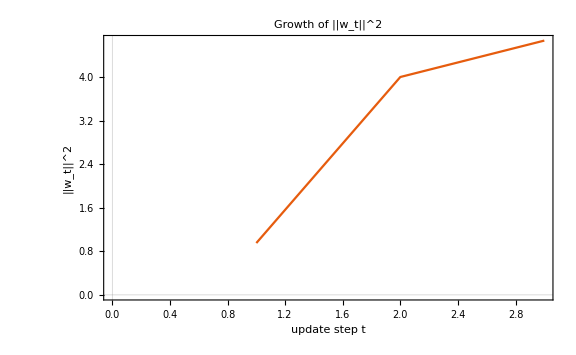

```mathematica
ListLinePlot[
 wNormSq,
 AxesLabel -> {"update step t", "||w_t||^2"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Growth of ||w_t||^2",
 ImageSize -> Large
]
```

## Non-separable data: XOR

```mathematica
Xxor = {
  {1., 1.},
  {1., -1.},
  {-1., 1.},
  {-1., -1.}
}
```

{{1.,1.},{1.,-1.},{-1.,1.},{-1.,-1.}}

```mathematica
yxor = {1, -1, -1, 1}
```

{1,-1,-1,1}

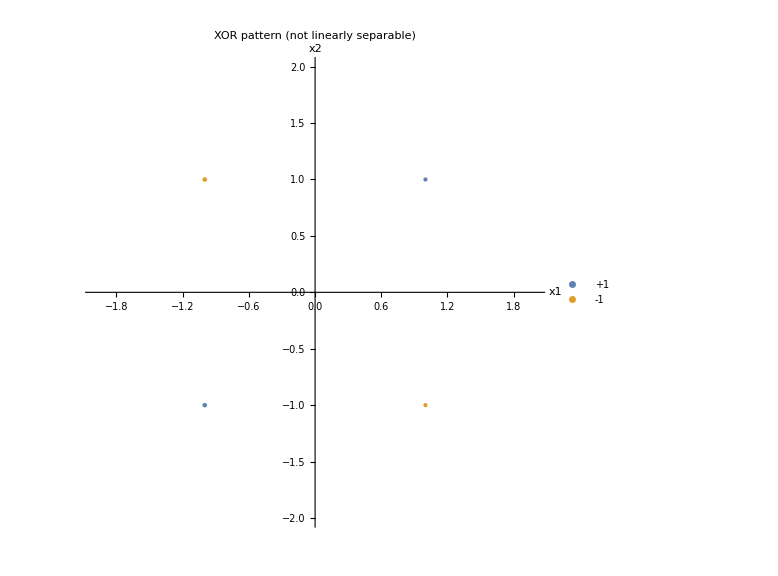

```mathematica
ListPlot[
 {
  Pick[Xxor, UnitStep[yxor], 1],
  Pick[Xxor, UnitStep[-yxor], 1]
 },
 PlotStyle -> {PointSize[Large], PointSize[Large]},
 PlotLegends -> {"+1", "-1"},
 AxesLabel -> {"x1", "x2"},
 PlotRange -> {{-2, 2}, {-2, 2}},
 PlotLabel -> "XOR pattern (not linearly separable)",
 ImageSize -> Large,
 AspectRatio -> 1
]
```

```mathematica
resultXor = perceptronTrain[Xxor, yxor, 50]
```

<|wFinal→{0.,0.},bFinal→0.,historyW→{{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.},{1.,1.},{0.,2.},{1.,1.},{0.,0.}},historyB→{1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.,1.,0.,-1.,0.},historyWDotWStar→{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]},historyWNormSq→{2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.},mistakesPerEpoch→{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},totalUpdates→200|>

```mathematica
wXor = resultXor["wFinal"]
```

{0.,0.}

```mathematica
bXor = resultXor["bFinal"]
```

0.

```mathematica
mistakesXor = resultXor["mistakesPerEpoch"]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
totalUpdatesXor = resultXor["totalUpdates"]
```

200

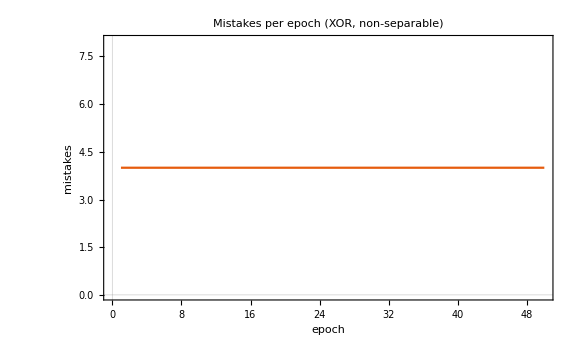

```mathematica
ListLinePlot[
 mistakesXor,
 AxesLabel -> {"epoch", "mistakes"},
 PlotTheme -> "Scientific",
 PlotLabel -> "Mistakes per epoch (XOR, non-separable)",
 ImageSize -> Large
]
```

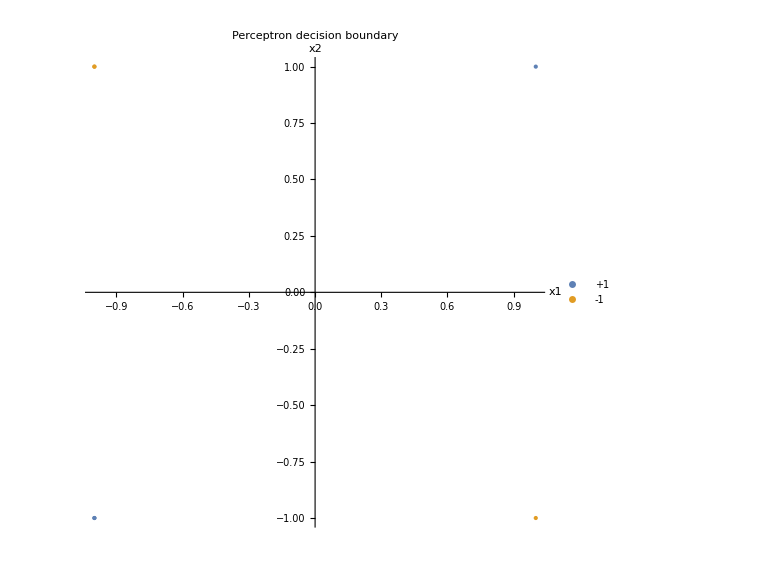

```mathematica
plotDecisionBoundary[wXor, bXor, Xxor, yxor]
```